```mathematica
q=Import["/home/lenny/Dropbox/Current/Blog/delays.csv"];
```

```mathematica
r=Import["/home/lenny/Dropbox/Current/Blog/delayshalf.csv"];
```

```mathematica
s=Import["/home/lenny/Dropbox/Current/Blog/delays1yr.csv"];
```

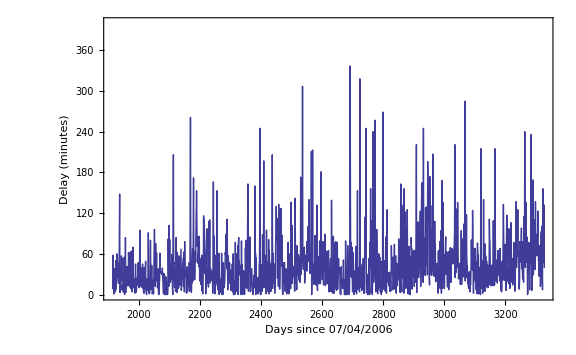

```mathematica
ListLinePlot[Table[{q[[i,1]],q[[i,2]]},{i,1,Length[q]}],PlotRange->{0,400},ImageSize->Large,Frame->True,{FrameStyle->Directive[Black],FrameLabel->{Style["Days since 07/04/2006",Large,Bold],Style["Delay (minutes)",Large,Bold],,}}]
```

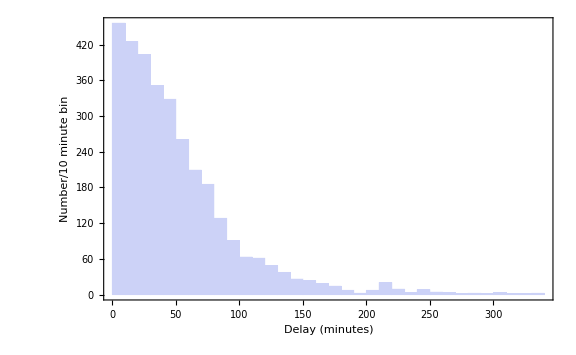

```mathematica
Histogram[Transpose[q][[2]],ImageSize->Large,Frame->True,{FrameStyle->Directive[Black],FrameLabel->{Style["Delay (minutes)",Large,Bold],Style["Number/10 minute bin",Large,Bold],,}}]
```

```mathematica
Count[Transpose[q][[2]],x_/;x>2]
```

3039

```mathematica
Length[Transpose[q][[2]]]
```

3199

```mathematica
p[t_] :=Count[Transpose[q][[2]],x_/;x≥ t]/Length[Transpose[q][[2]]]
n[t_] :=Count[Transpose[r][[2]],x_/;x≥ t]/Length[Transpose[r][[2]]]
```

```mathematica
o[t_] := Count[Transpose[s][[2]],x_/;x≥ t]/Length[Transpose[s][[2]]]
```

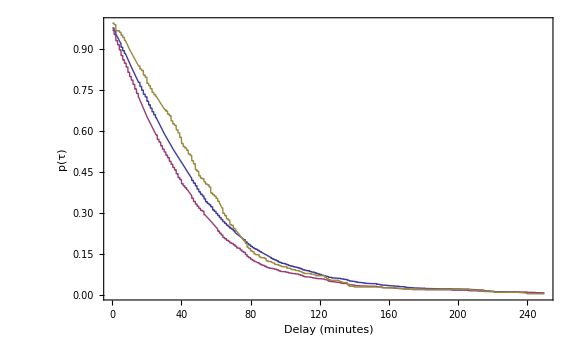

```mathematica
Plot[{p[t],n[t],o[t]},{t,0,250},ImageSize->Large,Frame->True,{FrameStyle->Directive[Black],FrameLabel->{Style["Delay (minutes)",Large,Bold],Style["p(τ)",Large,Bold],,}}]
```

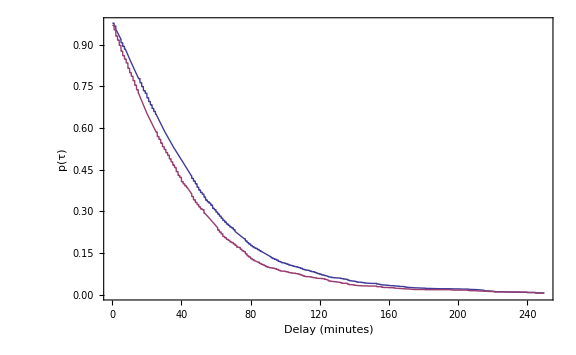

```mathematica
Plot[{p[t],n[t]},{t,0,250},ImageSize->Large,Frame->True,{FrameStyle->Directive[Black],FrameLabel->{Style["Delay (minutes)",Large,Bold],Style["p(τ)",Large,Bold],,}}]
```